```mathematica
simplifiedTable2=
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,tableTotalppibar//inGroupsOf[2]}];
simplifiedTable4=
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,tableTotalppibar//inGroupsOf[4]}];
simplifiedTable6=
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,tableTotalppibar//inGroupsOf[6]}];
simplifiedTable10=
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,tableTotalppibar//inGroupsOf[10]}];
```

```mathematica
simplifiedTable10//Length
```

48

```mathematica
evenSpacedTable=Table[{x,Interpolation[simplifiedTable10,x,InterpolationOrder->1]},{x,1.15,3.89,(3.89-1.15)/120}]
```

{{1.15,20.3919},{1.17283,35.1056},{1.19567,53.4896},{1.2185,67.8302},{1.24133,61.3948},{1.26417,47.1339},{1.287,36.1912},{1.30983,29.9881},{1.33267,26.8335},{1.3555,26.5702},{1.37833,27.7574},{1.40117,28.5599},{1.424,30.0137},{1.44683,32.8038},{1.46967,37.3226},{1.4925,44.0601},{1.51533,45.7762},{1.53817,42.1849},{1.561,37.6042},{1.58383,35.9693},{1.60667,38.7317},{1.6295,45.5506},{1.65233,53.6462},{1.67517,58.0236},{1.698,54.3861},{1.72083,47.0179},{1.74367,41.6299},{1.7665,38.2877},{1.78933,36.5429},{1.81217,36.1408},{1.835,36.1086},{1.85783,36.3178},{1.88067,36.1149},{1.9035,35.7958},{1.92633,35.3629},{1.94917,34.9317},{1.972,34.5016},{1.99483,34.3947},{2.01767,34.5755},{2.0405,34.7563},{2.06333,34.9371},{2.08617,35.1311},{2.109,35.3531},{2.13183,35.575},{2.15467,35.797},{2.1775,35.9509},{2.20033,35.7146},{2.22317,35.4783},{2.246,35.2419},{2.26883,35.0056},{2.29167,34.7693},{2.3145,34.5329},{2.33733,34.2954},{2.36017,34.0514},{2.383,33.8073},{2.40583,33.5632},{2.42867,33.3192},{2.4515,33.0751},{2.47433,32.831},{2.49717,32.587},{2.52,32.381},{2.54283,32.278},{2.56567,32.1749},{2.5885,32.0718},{2.61133,31.9688},{2.63417,31.8657},{2.657,31.7626},{2.67983,31.6595},{2.70267,31.5565},{2.7255,31.4534},{2.74833,31.3503},{2.77117,31.244},{2.794,31.1329},{2.81683,31.0218},{2.83967,30.9108},{2.8625,30.7997},{2.88533,30.6887},{2.90817,30.5776},{2.931,30.4666},{2.95383,30.3555},{2.97667,30.2445},{2.9995,30.1334},{3.02233,30.0257},{3.04517,29.9217},{3.068,29.8176},{3.09083,29.7135},{3.11367,29.6095},{3.1365,29.5054},{3.15933,29.4014},{3.18217,29.2973},{3.205,29.1932},{3.22783,29.0978},{3.25067,29.0211},{3.2735,28.9445},{3.29633,28.8678},{3.31917,28.7911},{3.342,28.7144},{3.36483,28.6378},{3.38767,28.5611},{3.4105,28.4844},{3.43333,28.4077},{3.45617,28.3311},{3.479,28.2806},{3.50183,28.2432},{3.52467,28.2058},{3.5475,28.1684},{3.57033,28.131},{3.59317,28.0936},{3.616,28.0562},{3.63883,28.0188},{3.66167,27.9814},{3.6845,27.944},{3.70733,27.9066},{3.73017,27.8692},{3.753,27.8318},{3.77583,27.7944},{3.79867,27.757},{3.8215,27.7196},{3.84433,27.6822},{3.86717,27.6448},{3.89,27.6074}}

```mathematica
simplifiedTable10
```

{{1.14951,20.079},{1.17985,39.626},{1.19826,55.765},{1.21347,67.46},{1.22429,68.256},{1.23638,64.29},{1.2491,56.853},{1.25938,50.3},{1.26875,44.106},{1.2819,37.986},{1.30013,31.567},{1.31799,28.661},{1.33668,26.334},{1.35995,26.626},{1.38657,28.264},{1.40961,28.731},{1.43276,30.794},{1.46045,34.748},{1.48196,40.758},{1.49358,44.4},{1.50756,45.869},{1.52214,45.695},{1.5405,41.674},{1.55936,37.722},{1.58452,35.92},{1.60694,38.767},{1.63085,45.957},{1.65042,53.107},{1.66833,58.163},{1.68544,57.814},{1.70673,52.005},{1.72801,44.482},{1.75789,39.04},{1.78575,36.606},{1.82118,35.982},{1.85786,36.318},{1.89199,36.014},{1.93513,35.196},{1.98275,34.299},{2.07885,35.06},{2.17411,35.986},{2.33387,34.3325},{2.51383,32.4089},{2.7617,31.29},{3.01139,30.0756},{3.22066,29.1219},{3.46375,28.3056},{3.89758,27.595}}

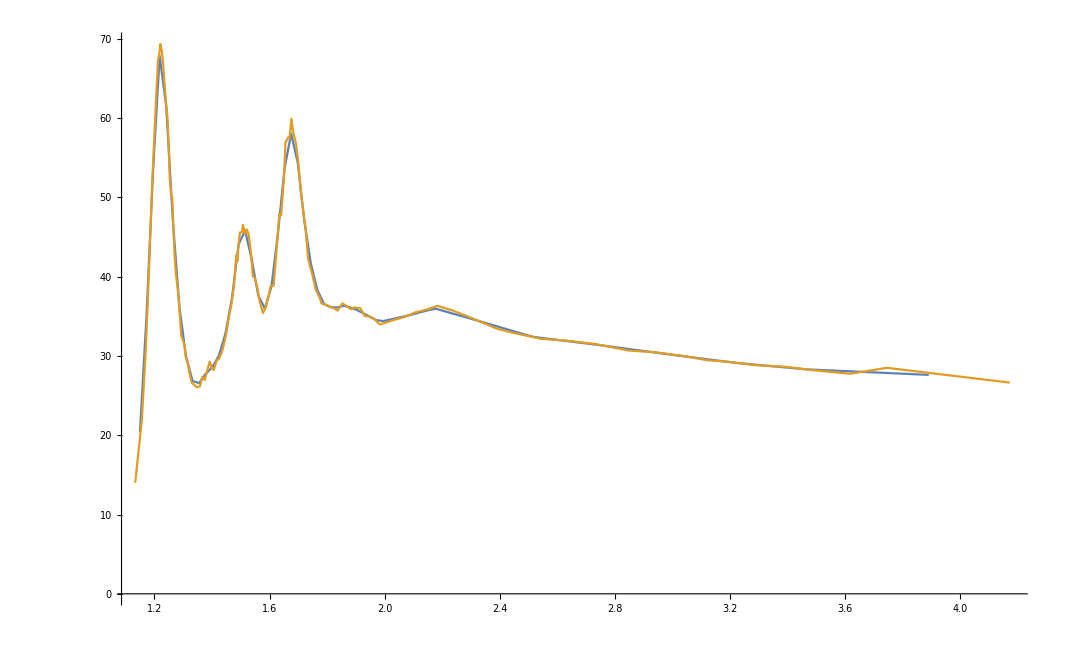

```mathematica
ListLinePlot[{evenSpacedTable,simplifiedTable4},PlotRange->All]
```

```mathematica
tableTotalppibar={pLabInv[m0@pi,m0@N938,#[[1]]],#[[2]]}&/@
{{0.09875,8.8700},{0.16000,13.600},{0.16520,15.800},{0.17600,17.700},{0.18101,21.000},{0.18900,21.200},{0.18980,23.120},{0.19100,22.200},{0.20400,28.000},{0.20600,29.300},{0.20930,31.000},{0.21220,33.740},{0.21870,38.440},{0.21885,33.400},{0.22000,38.600},{0.22200,39.300},{0.22740,44.480},{0.23063,42.700},{0.23413,46.900},{0.23600,47.700},{0.23645,52.000},{0.23800,50.300},{0.24330,55.350},{0.24684,48.100},{0.25100,58.200},{0.25300,59.100},{0.25371,55.300},{0.25599,60.000},{0.26021,56.400},{0.26168,62.900},{0.26460,67.900},{0.26600,66.200},{0.26800,68.100},{0.27040,70.260},{0.27071,67.500},{0.27520,63.000},{0.27536,67.200},{0.27600,71.000},{0.27632,62.700},{0.27920,70.740},{0.28100,71.900},{0.28285,67.200},{0.28300,72.200},{0.28303,66.000},{0.28637,65.900},{0.29033,67.700},{0.29100,70.600},{0.29260,69.760},{0.29303,63.500},{0.29552,67.800},{0.29600,68.800},{0.29800,68.800},{0.30242,64.000},{0.30297,64.600},{0.30407,63.100},{0.30600,65.500},{0.30760,63.800},{0.31100,62.300},{0.31293,59.300},{0.31300,62.700},{0.31811,58.700},{0.31930,59.430},{0.31941,57.200},{0.32050,64.000},{0.32330,55.600},{0.32594,55.500},{0.32700,55.000},{0.32800,56.400},{0.32812,54.500},{0.32848,52.200},{0.33138,52.100},{0.33367,50.200},{0.33571,50.500},{0.33728,48.200},{0.33788,52.900},{0.34074,49.000},{0.34100,48.800},{0.34220,58.000},{0.34300,48.800},{0.34436,44.500},{0.34500,47.060},{0.34797,44.900},{0.34867,46.100},{0.34985,48.300},{0.35144,42.700},{0.35298,43.500},{0.35491,43.100},{0.35600,42.900},{0.35800,41.500},{0.35853,41.000},{0.36201,39.300},{0.36549,39.800},{0.36911,38.800},{0.36950,38.460},{0.37100,38.100},{0.37227,38.200},{0.37274,36.800},{0.37300,38.300},{0.37812,35.600},{0.38176,36.500},{0.38351,33.400},{0.38600,33.300},{0.38890,31.100},{0.39430,32.400},{0.39971,31.600},{0.40100,31.100},{0.40512,30.500},{0.40626,33.000},{0.40640,29.970},{0.41055,29.300},{0.41500,30.830},{0.41600,29.000},{0.41612,28.900},{0.42156,28.100},{0.42407,30.200},{0.42716,28.700},{0.42736,27.890},{0.43000,27.800},{0.43262,27.000},{0.43500,28.190},{0.43809,26.200},{0.44311,26.800},{0.44312,26.400},{0.44500,27.000},{0.44935,26.000},{0.45500,26.730},{0.45881,25.980},{0.46000,26.600},{0.46065,24.900},{0.46925,26.730},{0.47400,26.360},{0.47500,26.180},{0.47723,25.200},{0.47968,25.980},{0.48900,26.400},{0.49008,27.000},{0.49320,26.700},{0.49500,26.500},{0.49900,27.040},{0.49903,28.900},{0.50047,27.230},{0.51085,26.500},{0.51300,27.490},{0.51500,26.700},{0.53155,27.570},{0.53500,27.190},{0.53625,34.000},{0.54188,28.400},{0.54452,29.500},{0.54705,28.060},{0.54808,29.440},{0.54911,27.000},{0.55000,28.520},{0.55500,27.880},{0.56251,27.150},{0.56500,29.360},{0.57281,27.000},{0.57500,28.810},{0.57600,29.550},{0.57630,32.600},{0.57796,29.110},{0.58310,29.310},{0.58765,30.000},{0.59132,29.960},{0.59338,31.100},{0.59500,30.960},{0.60878,29.910},{0.61400,30.190},{0.61742,34.600},{0.62200,32.800},{0.62416,30.710},{0.63200,32.140},{0.63686,35.900},{0.63892,34.900},{0.63952,33.340},{0.64259,34.980},{0.65000,34.020},{0.65100,36.650},{0.65486,34.840},{0.65820,40.000},{0.66400,39.590},{0.66800,37.560},{0.67019,37.790},{0.67300,40.690},{0.67530,37.460},{0.68200,43.560},{0.68300,46.000},{0.68487,43.600},{0.68551,39.740},{0.68700,41.590},{0.68891,44.600},{0.69000,41.880},{0.69265,44.820},{0.69300,45.180},{0.69367,42.300},{0.69571,42.990},{0.69911,49.000},{0.70081,42.970},{0.70200,45.680},{0.70500,44.580},{0.71100,46.310},{0.71326,45.800},{0.71500,44.700},{0.71610,45.550},{0.71711,45.070},{0.71800,46.000},{0.71832,49.600},{0.72300,45.460},{0.72650,45.500},{0.73035,44.700},{0.73100,45.900},{0.73646,45.430},{0.73866,45.100},{0.73981,50.000},{0.74000,44.140},{0.74100,44.590},{0.74257,45.290},{0.74300,44.100},{0.75681,44.100},{0.75914,48.300},{0.76000,41.600},{0.76500,41.620},{0.76611,44.400},{0.77002,44.470},{0.77400,40.380},{0.77500,41.540},{0.77714,39.600},{0.77800,38.630},{0.77944,45.300},{0.78847,39.200},{0.79000,38.220},{0.79100,36.630},{0.79237,39.160},{0.79971,42.100},{0.80400,36.670},{0.80760,37.060},{0.81200,36.480},{0.81500,35.730},{0.81800,36.170},{0.81996,39.000},{0.82400,35.800},{0.83300,35.120},{0.84000,35.630},{0.84326,35.100},{0.84500,36.100},{0.84715,34.900},{0.85100,36.090},{0.85952,37.100},{0.86500,36.660},{0.86949,36.700},{0.87000,38.640},{0.87300,38.450},{0.87363,37.600},{0.87754,37.430},{0.88300,40.230},{0.89000,39.940},{0.89387,37.400},{0.89779,37.380},{0.90100,41.600},{0.90386,39.000},{0.90700,44.410},{0.91500,44.210},{0.91810,39.000},{0.92020,43.900},{0.92611,40.200},{0.93100,49.580},{0.93900,51.580},{0.94000,50.290},{0.94041,48.500},{0.94429,47.900},{0.94532,46.370},{0.94835,48.200},{0.95455,50.000},{0.96147,55.200},{0.96500,55.560},{0.96553,48.130},{0.96555,54.600},{0.96958,55.130},{0.97100,57.780},{0.98070,60.100},{0.98574,53.320},{0.98800,59.880},{0.99000,58.540},{0.99376,58.600},{0.99584,54.200},{0.99600,60.090},{0.99681,56.000},{0.99786,59.220},{1.00094,61.200},{1.00200,60.580},{1.01500,58.090},{1.01600,59.750},{1.01603,56.760},{1.01610,57.800},{1.02007,58.460},{1.02114,60.500},{1.02700,57.800},{1.04000,55.180},{1.04019,59.300},{1.04420,54.500},{1.04529,55.170},{1.04832,55.020},{1.05000,53.800},{1.06045,54.400},{1.06500,50.220},{1.06940,50.400},{1.07354,50.670},{1.07500,49.750},{1.07555,48.820},{1.08158,51.800},{1.08900,46.690},{1.09000,45.630},{1.09572,45.700},{1.09880,44.700},{1.10100,44.410},{1.10173,48.900},{1.10277,44.840},{1.11500,41.410},{1.11588,41.520},{1.12700,41.020},{1.14000,39.350},{1.14108,42.800},{1.14110,39.600},{1.14510,39.540},{1.15100,39.290},{1.16500,37.970},{1.16600,38.150},{1.17600,38.140},{1.18126,38.300},{1.19000,37.260},{1.19500,37.190},{1.19545,36.660},{1.20100,37.180},{1.20144,37.600},{1.20330,35.900},{1.20753,35.770},{1.21500,36.380},{1.22600,36.760},{1.24000,36.120},{1.24175,36.500},{1.25100,36.570},{1.26500,36.190},{1.27500,36.450},{1.27780,35.500},{1.28100,36.420},{1.28193,36.000},{1.28199,35.520},{1.29000,36.160},{1.29608,34.450},{1.31200,36.560},{1.31500,36.230},{1.32118,35.600},{1.33200,36.630},{1.34000,36.570},{1.34900,36.640},{1.35500,36.610},{1.36500,36.390},{1.38000,36.680},{1.38845,35.700},{1.39000,36.130},{1.39303,34.600},{1.39561,35.720},{1.39900,36.650},{1.40900,36.620},{1.41500,35.880},{1.42051,35.900},{1.43300,36.540},{1.44000,36.110},{1.45100,36.490},{1.46500,35.630},{1.47600,36.070},{1.49000,35.820},{1.49400,36.060},{1.49607,33.480},{1.50088,35.500},{1.51500,35.060},{1.52097,35.300},{1.53100,35.540},{1.54000,34.630},{1.54115,34.500},{1.56500,34.390},{1.57200,35.080},{1.58119,34.700},{1.59000,34.000},{1.59548,31.810},{1.60400,34.750},{1.62139,34.700},{1.62200,34.620},{1.67200,34.640},{1.68155,34.300},{1.71900,34.700},{1.75983,34.300},{1.77300,35.080},{1.78500,35.110},{1.82099,34.000},{1.82100,35.510},{1.85100,35.490},{1.86900,35.580},{1.87913,34.800},{1.91600,36.030},{1.92026,35.200},{1.95100,36.080},{1.96700,36.180},{2.00010,35.700},{2.01600,36.380},{2.05000,36.420},{2.06700,36.340},{2.10200,36.100},{2.11979,35.400},{2.16800,36.060},{2.21700,35.770},{2.26000,35.480},{2.26600,35.440},{2.36600,34.630},{2.41400,34.350},{2.47000,33.800},{2.52000,34.055},{2.52200,33.530},{2.56800,33.320},{2.61400,32.950},{2.62000,33.468},{2.66500,32.890},{2.72000,33.017},{2.75000,32.500},{2.82000,32.758},{2.92000,32.546},{3.02000,32.411},{3.10010,30.900},{3.12000,32.299},{3.15000,31.300},{3.22000,32.174},{3.32000,31.973},{3.40000,31.400},{3.42000,31.746},{3.52000,31.569},{3.62000,31.334},{3.72000,31.064},{3.82000,30.901},{3.90000,30.000},{3.93000,30.739},{4.03000,30.519},{4.10000,30.800},{4.13000,30.363},{4.23000,30.170},{4.33000,30.058},{4.43000,29.902},{4.50000,30.200},{4.53000,29.744},{4.63000,29.600},{4.63747,29.400},{4.73000,29.487},{4.83000,29.360},{4.90000,29.600},{4.93000,29.237},{4.95000,29.100},{5.03000,29.120},{5.13000,28.988},{5.23000,28.881},{5.33000,28.766},{5.44000,28.680},{5.54000,28.586},{5.64000,28.450},{5.74000,28.355},{5.75000,29.100},{5.84000,28.256},{5.94000,28.149},{6.00000,28.500},{6.04000,28.072},{6.24000,27.884},{6.44000,27.704},{6.64000,27.518},{6.65000,27.900},{6.84000,27.356},{6.94000,27.236},{7.00000,28.400},{7.19863,31.000},{8.00000,27.640},{8.05000,28.400},{9.20000,25.000},{10.00000,25.500}};
tableElasticppibar={pLabInv[m0@pi,m0@N938,#[[1]]],#[[2]]}&/@
{{0.09875,1.8470},{0.14956,2.9000},{0.21648,9.6000},{0.21885,11.300},{0.22828,12.800},{0.24684,17.000},{0.25599,20.100},{0.26733,21.400},{0.27071,22.500},{0.27520,21.200},{0.29303,22.500},{0.30297,26.400},{0.32050,28.700},{0.33138,19.500},{0.33571,16.000},{0.33788,17.400},{0.35052,15.100},{0.35190,20.800},{0.37800,12.290},{0.38261,12.400},{0.40400,10.100},{0.40626,13.800},{0.40800,10.410},{0.42188,11.400},{0.42700,9.0000},{0.44888,10.300},{0.45200,8.9000},{0.47100,9.2000},{0.49008,10.420},{0.50900,9.1500},{0.52300,9.8000},{0.52845,11.400},{0.53155,11.400},{0.54700,9.9900},{0.54911,13.000},{0.55600,10.240},{0.56500,10.800},{0.57281,12.190},{0.58200,16.200},{0.58600,11.340},{0.60900,12.860},{0.61390,13.710},{0.61698,13.900},{0.62500,12.190},{0.64054,14.800},{0.65700,13.920},{0.65793,16.200},{0.65800,15.320},{0.67530,16.980},{0.68300,18.900},{0.68700,17.070},{0.69061,18.860},{0.69900,19.070},{0.70692,19.950},{0.71399,20.500},{0.72628,19.870},{0.73100,18.900},{0.73257,16.600},{0.74257,19.400},{0.75000,19.910},{0.76189,18.940},{0.77500,17.560},{0.77714,17.190},{0.77827,16.100},{0.79800,14.910},{0.82586,15.750},{0.83803,14.900},{0.84800,13.200},{0.84954,14.100},{0.85400,14.470},{0.87466,14.400},{0.89417,25.100},{0.90386,14.800},{0.91903,14.100},{0.92400,18.800},{0.94349,21.800},{0.95500,21.620},{0.95947,18.000},{0.97900,23.160},{0.98977,26.600},{0.99500,26.420},{0.99988,22.200},{1.00290,26.580},{1.00400,24.220},{1.01704,27.300},{1.02400,26.300},{1.03016,18.600},{1.04200,26.010},{1.04220,24.600},{1.04529,26.700},{1.06700,23.650},{1.08000,25.100},{1.08059,19.100},{1.08800,19.480},{1.09068,20.000},{1.09111,14.600},{1.10600,17.950},{1.12091,19.820},{1.12339,17.700},{1.12500,18.290},{1.13099,22.000},{1.16400,13.660},{1.16500,15.010},{1.17400,15.730},{1.21400,12.450},{1.21659,14.100},{1.23000,14.600},{1.25000,13.310},{1.26000,13.800},{1.27900,12.800},{1.32300,13.090},{1.33630,12.000},{1.33900,12.627},{1.34100,12.730},{1.34200,12.380},{1.34300,13.507},{1.34500,12.714},{1.34700,12.987},{1.34900,13.401},{1.35100,13.384},{1.35300,12.394},{1.35500,12.763},{1.35700,12.724},{1.35900,12.851},{1.36100,12.507},{1.36300,12.430},{1.36500,12.367},{1.36700,12.395},{1.36900,13.332},{1.37100,12.491},{1.37300,13.035},{1.37500,12.852},{1.37700,12.040},{1.37900,12.673},{1.38000,15.000},{1.38100,12.488},{1.38200,12.530},{1.38300,12.286},{1.38500,12.670},{1.38700,12.662},{1.38900,13.354},{1.39100,13.054},{1.39300,12.626},{1.39500,12.126},{1.39700,12.651},{1.39900,12.956},{1.40100,12.606},{1.40300,12.361},{1.40500,12.340},{1.40700,12.091},{1.40900,12.130},{1.41100,11.937},{1.41300,12.712},{1.41500,12.478},{1.41700,12.510},{1.41900,12.521},{1.42100,12.321},{1.42300,12.271},{1.42500,12.594},{1.42700,12.536},{1.42900,12.260},{1.43100,12.407},{1.43300,12.346},{1.43500,12.532},{1.43700,12.407},{1.43900,12.266},{1.44100,12.167},{1.44300,12.266},{1.44500,11.950},{1.44700,11.776},{1.44900,11.907},{1.45100,12.042},{1.45300,11.786},{1.45500,11.568},{1.45700,11.246},{1.45900,11.767},{1.46100,12.017},{1.46300,11.754},{1.46500,11.413},{1.46700,11.436},{1.46900,11.206},{1.47000,10.870},{1.47100,10.828},{1.47300,11.052},{1.47500,11.119},{1.47700,11.575},{1.47900,11.645},{1.48100,11.434},{1.48300,12.639},{1.48500,11.643},{1.48700,11.702},{1.48900,11.210},{1.49100,11.502},{1.49300,11.313},{1.49500,11.368},{1.49700,11.523},{1.49900,11.163},{1.50300,11.690},{1.50310,10.000},{1.50900,10.390},{1.56700,10.210},{1.59000,9.6500},{1.60000,9.0000},{1.60300,9.8200},{1.71000,10.400},{1.85000,11.100},{2.00000,7.3400},{2.01000,7.9400},{2.10000,9.6900},{2.14000,9.3000},{2.26000,8.9100},{2.29000,8.5000},{2.70000,7.7000},{2.75000,7.2000},{2.77000,7.2000},{2.79990,7.8000},{3.00000,7.5700},{3.15000,6.1000},{3.25000,7.3000},{3.65000,6.9700},{3.92000,6.8400},{4.00000,6.6200},{4.13000,5.6000},{4.16000,5.7700},{4.50000,6.2100},{4.63747,3.5000},{4.75000,4.7000},{4.95000,6.1000},{5.00000,5.8500},{5.17000,5.6000},{6.00000,5.3000},{7.00000,5.1300},{8.00000,5.0700},{8.90020,4.8200},{9.99990,4.5900},{10.8000,4.7700},{11.2000,4.4300},{13.0000,4.7200},{15.0000,4.6200},{15.9000,4.2000},{16.0000,4.0800},{16.2000,4.3600},{17.0000,4.1100},{18.9000,4.3900},{25.2000,3.3500},{32.8200,3.2170},{35.3900,3.5500},{40.1000,3.3200},{42.0200,3.3590},{45.3400,3.5060},{48.6100,3.4560},{50.0000,3.4800},{50.9600,3.4140},{54.7400,3.2670},{55.1000,3.0450},{70.0000,3.3900},{100.000,3.2800},{140.000,3.3600},{147.000,3.2400},{175.000,3.3800},{200.000,3.3200},{205.000,3.1800},{360.000,3.6100}};
```

```mathematica
σTotalppibar[eCM_]:=Piecewise[{
{0.,eCM≤m0@pi+m0@N938},
{σRes[N938,1/2,pi,-1,eCM],eCM<1.8},
{Interpolation[tableTotalppibar,eCM,InterpolationOrder->1],eCM≤3.5}
},13.7*eCM^0.158+35.9eCM^-0.90
];
σResppibar[eCM_]:=If[eCM≤m0@pi+m0@N938,0.,σRes[N938,1/2,pi,-1,eCM]];
σFullElasticppibar[eCM_]:=Piecewise[{
{0.,eCM≤m0@pi+m0@N938},
{σResEl[N938,1/2,pi,-1,eCM],eCM<1.75},
{Interpolation[tableElasticppibar,eCM,InterpolationOrder->1],eCM≤2.0}
},fitHERA[pLab[m0@pi,m0@N938,eCM],1.76,11.2,-0.64,0.043,0.]
];
σResElasticppibar[eCM_]:=If[eCM≤m0@pi+m0@N938,0.,σResEl[N938,1/2,pi,-1,eCM]];
σElasticppibar[eCM_]:=If[eCM<1.96,0.,σFullElasticppibar[eCM]-σResElasticppibar[eCM]];
σStringppibar[eCM_]:=If[eCM<1.8,0.,σTotalppibar[eCM]-σElasticppibar[eCM]-σResppibar[eCM]];
```

```mathematica
ptsTableppibar=Table[{p,Interpolation[tableTotalppibar,pLabInv[m0@pi,m0@N938,p],InterpolationOrder->1]},{p,m0@pi+m0@N938,5.,0.01}];
```

```mathematica
ptsTotalppibar=Monitor[
Table[{p,σTotalppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

```mathematica
ptsResppibar=Monitor[
Table[{p,σResppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ptsElasticppibar=Monitor[
Table[{p,σElasticppibar@pLabInv[m0@pi,m0@N938,p]},{p,1.,5.,0.01}],
ProgressIndicator[p,{1.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ptsStringppibar=Monitor[
Table[{p,σStringppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

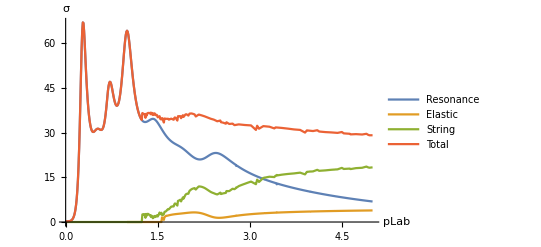

```mathematica
ListLinePlot[{ptsResppibar,ptsElasticppibar,ptsStringppibar,ptsTotalppibar},PlotRange->All,PlotLegends->{"Resonance","Elastic","String","Total"},AxesLabel->{"pLab","σ"}]
```

```mathematica
ptsFullElasticppibar=Monitor[
Table[{p,fitHERA[p,1.76,11.2,-0.64,0.043,0.]},{p,1.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

```mathematica
ptsResElasticppibar=Monitor[
Table[{p,σResElasticppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ptsNonresElasticppibar=Monitor[
Table[{p,σElasticppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

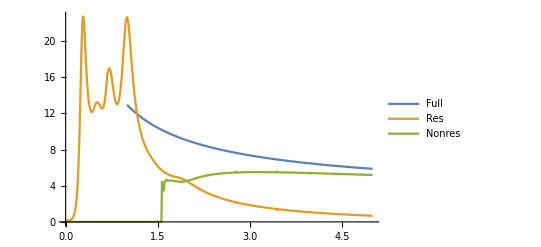

```mathematica
ListLinePlot[{ptsFullElasticppibar,ptsResElasticppibar,ptsNonresElasticppibar},PlotRange->All,PlotLegends->{"Full","Res","Nonres"}]
```